### Plot parameters

```mathematica
ft=Flatten
fs=FullSimplify
ff=First
fft[x_]:=First[Flatten[x]]
fontsize=9;
tmax=50;
cols=RGBColor/@{"#0e6692","#5a65b1","#ae52ac","#ed347c","#ff4a2e"}
```

Flatten

FullSimplify

First

{RGBColor[0.054901960784313725, 0.4, 0.5725490196078431],RGBColor[0.35294117647058826, 0.396078431372549, 0.6941176470588235],RGBColor[0.6823529411764706, 0.3215686274509804, 0.6745098039215687],RGBColor[0.9294117647058824, 0.20392156862745098, 0.48627450980392156],RGBColor[1., 0.2901960784313726, 0.1803921568627451]}

### Abstract models

Growth function: gives per capita growth rate, takes information about which variable, all variable densities (vars), optimal equilibrium frequency (eql), strength of balancing selection (q: at locus; q2: at genotype), growth rate (r) and carrying capacity (k).

```mathematica
σ=0.5;
alleles = {{1,1},{1,0},{0,1},{0,0}};
Vars = {AB[t],Ab[t],aB[t],ab[t]};
```

```mathematica
alleleFreq[n_,m_,vars_] := Total[vars[[Position[alleles[[All,m]],alleles[[n,m]]]//Flatten]]]/Total[vars];
```

```mathematica
recombination[n1_,vars1_,rec1_] := Module[{n = n1,vars = vars1,rec = rec1},index = Total/@Boole/@Map[Table[#[[i]] == alleles[[n]][[i]],{i,2}]&,alleles];
-rec*vars[[Position[index,2][[1]]]]*vars[[Position[index,0][[1]]]]+
rec*Times@@vars[[Position[index,1]//Flatten]]][[1]]
```

```mathematica
(*This form comes from simplifying much more complex form*)
```

```mathematica
(* Additive balancing selection *)

(*capitaGrowthAdditiveNFDS[n_,vars_,eql_,q_,r_,k_,q2_,ϵ_]:= r*(1-Total[vars]/k) +q*(eql-alleleFreq[n,1,vars] )+q*(eql-alleleFreq[n,2,vars])+q2*( eql*eql - vars[[n]]/Total[vars] )+ϵ If[(n==1)||(n==4),1,0]; (*epistasis for D^+*)*)
capitaGrowthAdditiveNFDS[n_,vars_,eql_,q_,r_,k_,q2_,ϵ_]:= r*(1-Total[vars]/k) +q*(eql-alleleFreq[n,1,vars] )+q*(eql-alleleFreq[n,2,vars])+q2*( eql*eql - vars[[n]]/Total[vars] )+ϵ If[(n==4),1,0];(*epistasis for AB*)

(*capitaGrowthMultiplicativeNFDS[n_,vars_,eql_,q_,r_,k_]:= r*(1-Total[vars]/k) *q^(eql-alleleFreq[n,1,vars] )*q^(eql-alleleFreq[n,2,vars]);*)
```

```mathematica
capitaGrowthAdditiveNFDS[1,Vars,0.5,q,r,k,q2,ϵ]+capitaGrowthAdditiveNFDS[4,Vars,0.5,q,r,k,q2,ϵ]-capitaGrowthAdditiveNFDS[2,Vars,0.5,q,r,k,q2,ϵ]-capitaGrowthAdditiveNFDS[3,Vars,0.5,q,r,k,q2,ϵ]/.q2->0//FullSimplify
```

ϵ

#### D equation

{2-ab[t]-aB[t]-Ab[t]-AB[t]-(aB[t]+AB[t])/(ab[t]+aB[t]+Ab[t]+AB[t])-(Ab[t]+AB[t])/(ab[t]+aB[t]+Ab[t]+AB[t])+1/2 (-1/4+AB[t]/(ab[t]+aB[t]+Ab[t]+AB[t])),2-ab[t]-aB[t]-Ab[t]-AB[t]-(ab[t]+Ab[t])/(ab[t]+aB[t]+Ab[t]+AB[t])-(Ab[t]+AB[t])/(ab[t]+aB[t]+Ab[t]+AB[t])+1/2 (-1/4+Ab[t]/(ab[t]+aB[t]+Ab[t]+AB[t])),2-ab[t]-aB[t]-Ab[t]-AB[t]-(ab[t]+aB[t])/(ab[t]+aB[t]+Ab[t]+AB[t])-(aB[t]+AB[t])/(ab[t]+aB[t]+Ab[t]+AB[t])+1/2 (-1/4+aB[t]/(ab[t]+aB[t]+Ab[t]+AB[t])),2-ab[t]-aB[t]-Ab[t]-AB[t]-(ab[t]+aB[t])/(ab[t]+aB[t]+Ab[t]+AB[t])-(ab[t]+Ab[t])/(ab[t]+aB[t]+Ab[t]+AB[t])+1/2 (-1/4+ab[t]/(ab[t]+aB[t]+Ab[t]+AB[t]))}

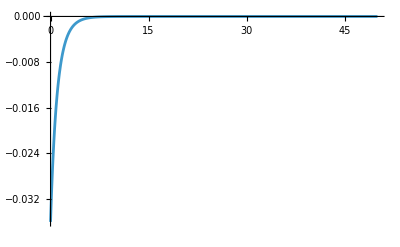

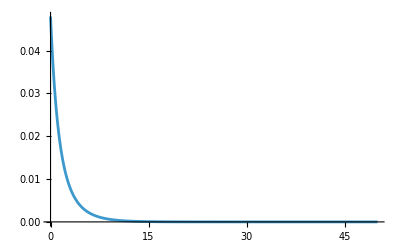

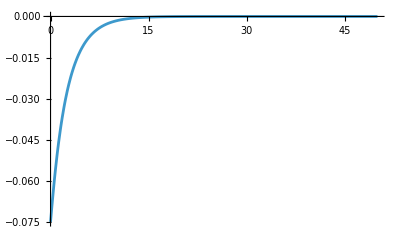

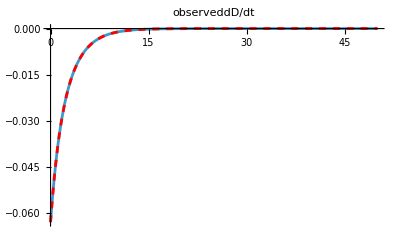

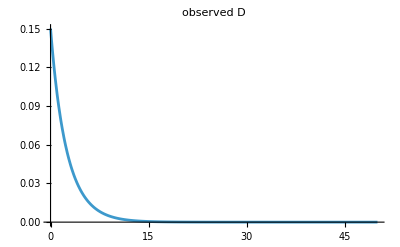

```mathematica
fAB[t_]:=((Vars[[1]])/Total[Vars])
fAb[t_]:=((Vars[[2]])/Total[Vars])
faB[t_]:=((Vars[[3]])/Total[Vars])
fab[t_]:=((Vars[[4]])/Total[Vars])
rVars=Table[capitaGrowthAdditiveNFDS[i,Vars,1/2,1,1,1,-1/2,0],{i,1,4,1}]

Subscript[s, A][t_] := rVars[[2]]-rVars[[4]];
Subscript[s, B][t_] := rVars[[3]] -rVars[[4]];
Subscript[s, AB][t_] := rVars[[1]] +rVars[[4]] - rVars[[2]] -rVars[[3]];
ss[t_]:= Subscript[s, A][t]fA[t]+Subscript[s, B][t]fB[t]+Subscript[s, AB][t]fAB[t];


DDD[t_] =D[DD[t]/.sol,t];


temp1=(Evaluate[Subscript[s, A][t]]+Evaluate[Subscript[s, B][t]]-2 Evaluate[ss[t]]) *Evaluate[DD[t]] ;

temp2=Evaluate[Subscript[s, AB][t]]*Evaluate[fAB[t]]*Evaluate[fab[t]];

temp3=-DD[t] * σ * Total[Vars];





Plot[Evaluate[temp1]/.sol,{t,0,tmax}, PlotRange->All]
Plot[Evaluate[temp2]/.sol,{t,0,tmax}, PlotRange->All]
Plot[Evaluate[temp3]/.sol,{t,0,tmax}, PlotRange->All]


Plot[Evaluate[temp1+temp2+temp3]/.sol,{t,0,tmax}, PlotRange->All, PlotLabel->"expecteddD/dt",PlotStyle->{Dashed,Red}];
Plot[Evaluate[DDD[t]]/.sol,{t,0,tmax},PlotRange->All, PlotLabel->"observeddD/dt"];
Show[%,%%]
Plot[DD[t]/.sol,{t,0,tmax},PlotRange->All, PlotLabel->"observed D"]
```

### gFDS and constant

```mathematica
recc=0.05
stepep=0.01
stepq2=0.01
minq2=-0.5
maxq2=0.5
mine=-0.5
maxe=0.5
```

0.05

0.01

0.01

-0.5

0.5

-0.5

0.5

## Figure 4 and S9

```mathematica
recc=0;
rainbow[z_]:=Blend[Reverse[{RGBColor["#C62E2E"],
RGBColor["#F95454"],
RGBColor["#DEDEDE"],
RGBColor["#77CDFF"],
RGBColor["#0D92F4"]}],z];
col[v_]=Opacity[0.8,rainbow[Rescale[v,{-01,1}]]];
sol2[q2_,ep_] := NDSolve[({Table[D[Vars[[i]],t]==Vars[[i]]*capitaGrowthAdditiveNFDS[i,Vars,1/2,1,1,1,q2,ep]+recombination[i,Vars,recc],{i,4}],{AB[0]==4/10,Ab[0] == 1/10,aB[0]==1/10,ab[0]==4/10}}//Flatten),Vars,{t,0,100000}];
D2[q2_,ep_] := If[fft[(DD[t]/.sol2[q2,ep] /.t->10000)]>0,fft[posDmax[t]/.sol2[q2,ep]/.t->10000],fft[-negDmax[t]/.sol2[q2,ep]/.t->10000]]

aa1=ListDensityPlot[Table[D2[q2,ep],{ep,mine,maxe,stepep}, {q2,minq2,maxq2,stepq2}], Frame->{{True, False},{True,False}}, FrameLabel->{{Style["ϵ",fontsizehm,Black],""},{Style["q_2",fontsizehm,Black],""}},  PlotRange->{All,All},DataRange->{{minq2,maxq2},{mine,maxe}},
 PlotLegends->BarLegend[{rainbow[Rescale[#1,{-1,1}]]&,{-1,1}}],
ColorFunctionScaling->False, 
ColorFunction->col    , Frame->{{True,False},{False,True}}, PlotRangePadding->None,InterpolationOrder->0]

sol2[q2_,ep_] := NDSolve[({Table[D[Vars[[i]],t]==Vars[[i]]*capitaGrowthAdditiveNFDS[i,Vars,1/2,1,1,1,q2,ep]+recombination[i,Vars,recc],{i,4}],{AB[0]==1/10,Ab[0] == 4/10,aB[0]==4/10,ab[0]==1/10}}//Flatten),Vars,{t,0,100000}];
D2[q2_,ep_] := If[fft[(DD[t]/.sol2[q2,ep] /.t->10000)]>0,fft[posDmax[t]/.sol2[q2,ep]/.t->100000],fft[-negDmax[t]/.sol2[q2,ep]/.t->10000]]

aa1=ListDensityPlot[Table[D2[q2,ep],{ep,mine,maxe,stepep}, {q2,minq2,maxq2,stepq2}], Frame->{{True, False},{True,False}}, FrameLabel->{{Style["ϵ",fontsizehm,Black],""},{Style["q_2",fontsizehm,Black],""}},  PlotRange->{All,All},DataRange->{{minq2,maxq2},{mine,maxe}},
 PlotLegends->BarLegend[{rainbow[Rescale[#1,{-1,1}]]&,{-1,1}}],
ColorFunctionScaling->False, 
ColorFunction->col    , Frame->{{True,False},{False,True}}, PlotRangePadding->None,InterpolationOrder->0]
```

Blend::argl: 1/2+v/2 should be a real number or a list of non-negative numbers, which has the same length as {color,color,color,color,color}.

-Graphics-

-Graphics-